# Morgan Nance Mathematica Exam Section A

```mathematica
(*A1*) a = List[1, Pi, 0.37, E^6 ];
```

```mathematica
(*A2*) b = a + 2 //N
```

{3.,5.14159,2.37,405.429}

```mathematica
(*A3*) c = List[9^17, Cos[13], Log[7], Factorial[7]];
```

```mathematica
(*A4*) c/2//N
```

{8.33859×10^15,0.453723,0.972955,2520.}

```mathematica
(*A5*) Range[37]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37}

```mathematica
(*A6*) d =Range[0,6,0.1];
```

```mathematica
(*A7*) Length[d]
```

61

```mathematica
(*A8*) myprimes=Table[Prime[ii],{ii,1,20}]
Export["myprimes.txt",myprimes]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

myprimes.txt

```mathematica
(*A9*) randomnumbers=Import["randomnumbers.txt","Data"];
```

```mathematica
(*A9*) 
Mean[randomnumbers[[;;10]]]
Mean[randomnumbers[[;;100]]]
Mean[randomnumbers[[;;300]]]
Mean[randomnumbers[[;;1000]]]
```

{2.16801}

{2.14317}

{2.14455}

{2.11627}

```mathematica
(*A10*) 
StandardDeviation[randomnumbers[[;;10]]]
StandardDeviation[randomnumbers[[;;100]]]
StandardDeviation[randomnumbers[[;;300]]]
StandardDeviation[randomnumbers[[;;1000]]]
```

{0.474534}

{0.492523}

{0.480228}

{0.496242}

```mathematica
(*A11*) 
Total[Table[(Mean[randomnumbers[[;;10]]]-randomnumbers[[ii]])^2,{ii,1,10}]]/9
Variance[randomnumbers[[;;10]]]
StandardDeviation[randomnumbers[[;;10]]]^2
```

{0.225182}

{0.225182}

{0.225182}

```mathematica
Section B
```

```mathematica
(*B1*) myprimesagain=Transpose[Import["myprimes.txt","Data"]]
```

{{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}}

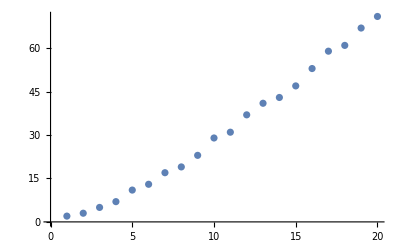

```mathematica
(*B1*) ListPlot[myprimesagain]
```

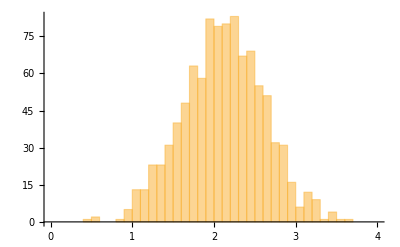

```mathematica
(*B2*) 
randomnumbers=Transpose[Import["randomnumbers.txt","Data"]];
Histogram[randomnumbers,{0.1},PlotRange->{{0,4},Automatic}](*Gaussian Distribution?*)
```

```mathematica
(*I don't understand B3. Math isn't my thing, so I don't even know what this is asking*)
```

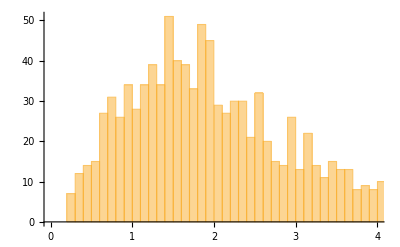

```mathematica
(*B4*) 
otherrandomnumbers=Transpose[Import["otherrandomnumbers.txt","Data"]];
Histogram[otherrandomnumbers,{0.1},PlotRange->{{0,4},Automatic}]
(*I don't know what distribution this would be*)
```

```mathematica
(*B5*)
dg[dgh2o_,m_,x_]:=dgh2o+(m*x)
k[dgh2o_,m_,x_,t_]:=Exp[(-dg[dgh2o,m,x])/(0.001987*t)]
fn[keq_]:=keq/(1+keq)
fd[keq_]:=1/(1+keq)
yn[an_,bn_,x_]:=an+bn*x
yd[ad_,bd_,x_]:=ad+bd*x
yobs[x_,dgh2o_,m_,t_,an_,bn_,ad_,bd_]:=(yn[an,bn,x]*fn[k[dgh2o,m,x,t]])+(yd[ad,bd,x]*fd[k[dgh2o,m,x,t]])
(*yobs=(yn*fn)+(yd*fd)*)
```

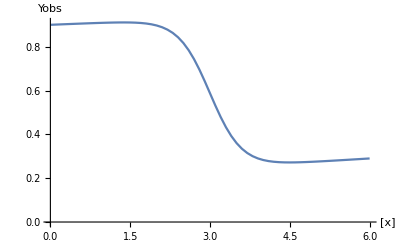

```mathematica
(*B4*)
ListLinePlot[Table[{x,yobs[x,-6,2,300,.9,.01,.2,.015]},{x,0,6,0.1}],AxesLabel->{"[x]","Yobs"}]
```

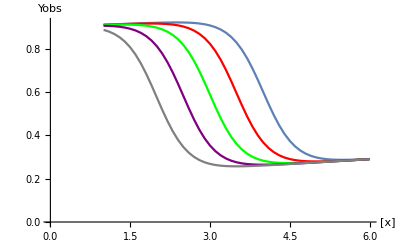

```mathematica
(*B6*)
one=ListLinePlot[Table[{x,yobs[x,-8,2,300,.9,.01,.2,.015]},{x,1,6,0.1}]];
two=ListLinePlot[Table[{x,yobs[x,-7,2,300,.9,.01,.2,.015]},{x,1,6,0.1}],PlotStyle->Red];
three=ListLinePlot[Table[{x,yobs[x,-6,2,300,.9,.01,.2,.015]},{x,1,6,0.1}],PlotStyle->Green];
four=ListLinePlot[Table[{x,yobs[x,-5,2,300,.9,.01,.2,.015]},{x,1,6,0.1}],PlotStyle->Purple];
five=ListLinePlot[Table[{x,yobs[x,-4,2,300,.9,.01,.2,.015]},{x,1,6,0.1}],PlotStyle->Gray];
Show[one,two,three,four,five,AxesLabel->{"[x]","Yobs"}]
```

```mathematica
(*B7*)
Plot3D[yobs[x,y,2,300,.9,.01,.2,.015],{x,1,6},{y,-8,0}]
```

-Graphics3D-

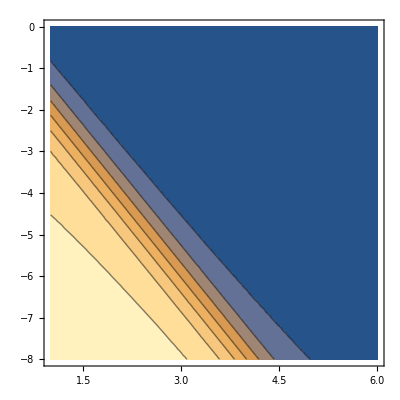

```mathematica
(*B8*)
ContourPlot[yobs[x,y,2,300,.9,.01,.2,.015],{x,1,6},{y,-8,0}]
```

```mathematica
Section C
```

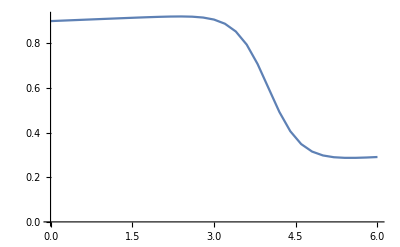

```mathematica
(*C1*)
data=Table[{x,yobs[x,-8,2,300,.9,.01,.2,.015]},{x,0,6,.2}];
ListLinePlot[ data ]
```

```mathematica
(*C1*)
error03=RandomVariate[NormalDistribution[0,.03],Length[data]];
error01=RandomVariate[NormalDistribution[0,.01],Length[data]];
error003=RandomVariate[NormalDistribution[0,.003],Length[data]];
error001=RandomVariate[NormalDistribution[0,.001],Length[data]];
```

```mathematica
(*C2*)
data03=data;
data03[[All,2]]=data[[All,2]]+error03;
data01=data;
data01[[All,2]]=data[[All,2]]+error01;
data003=data;
data003[[All,2]]=data[[All,2]]+error003;
data001=data;
data001[[All,2]]=data[[All,2]]+error001;
```

```mathematica
(*C2*)
R=0.001987;
T=300;
dg = dgh2o + m*x;
k=Exp[-dg/(R*T)];
fn=k/(1+k);
fd = 1/(1+k);
yn=an+bn*x;
yd=ad+bd*x;
yobs=yd*fd+yn*fn;
Clear[dgh2o]
```

```mathematica
(*C2 0.03 error*)
model03 = NonlinearModelFit[data03,yobs,{{dgh2o,-6},{m,2},{an,.9},{bn,0.01},{ad,0.2},{bd,0.015}},x];
model03["ParameterTable"]
model03["ParameterConfidenceIntervals"]
```

| Estimate | Standard Error | t-Statistic | P-Value
dgh2o | -6.6393 | 0.831809 | -7.98176 | 2.44953×10^-8
m | 1.63268 | 0.223358 | 7.30971 | 1.16902×10^-7
an | 0.892759 | 0.0147665 | 60.4584 | 1.26134×10^-28
bn | 0.0213228 | 0.0103408 | 2.062 | 0.0497469
ad | -0.144395 | 0.296466 | -0.487053 | 0.630464
bd | 0.0745657 | 0.0516094 | 1.44481 | 0.16093

{{-8.35244,-4.92616},{1.17267,2.0927},{0.862346,0.923171},{0.0000254662,0.0426202},{-0.754977,0.466188},{-0.0317259,0.180857}}

```mathematica
(*C1 0.01 error*)
model01 = NonlinearModelFit[data01,yobs,{{dgh2o,-6},{m,2},{an,.9},{bn,0.01},{ad,0.2},{bd,0.015}},x];
model01["ParameterTable"]
model01["ParameterConfidenceIntervals"]
```

| Estimate | Standard Error | t-Statistic | P-Value
dgh2o | -8.23063 | 0.351847 | -23.3927 | 1.63057×10^-18
m | 2.05329 | 0.0923095 | 22.2435 | 5.4335×10^-18
an | 0.905133 | 0.00418566 | 216.246 | 1.9786×10^-42
bn | 0.00634029 | 0.00259366 | 2.44454 | 0.0218955
ad | 0.24134 | 0.0630942 | 3.82508 | 0.00077534
bd | 0.00680824 | 0.0112669 | 0.604271 | 0.551109

{{-8.95527,-7.50599},{1.86318,2.24341},{0.896513,0.913754},{0.000998553,0.011682},{0.111396,0.371285},{-0.0163963,0.0300128}}

```mathematica
(*C1 0.003 error*)
model003 = NonlinearModelFit[data003,yobs,{{dgh2o,-6},{m,2},{an,.9},{bn,0.01},{ad,0.2},{bd,0.015}},x];
model003["ParameterTable"]
model003["ParameterConfidenceIntervals"]
```

| Estimate | Standard Error | t-Statistic | P-Value
dgh2o | -7.99635 | 0.118719 | -67.3556 | 8.60623×10^-30
m | 1.99696 | 0.0312716 | 63.8585 | 3.23935×10^-29
an | 0.899829 | 0.00149908 | 600.253 | 1.63743×10^-53
bn | 0.00942832 | 0.000943957 | 9.98808 | 3.28451×10^-10
ad | 0.184585 | 0.022964 | 8.03803 | 2.15488×10^-8
bd | 0.0177656 | 0.00409285 | 4.34065 | 0.000205778

{{-8.24086,-7.75185},{1.93256,2.06137},{0.896742,0.902917},{0.0074842,0.0113724},{0.13729,0.23188},{0.00933624,0.026195}}

```mathematica
(*C1 0.001 error*)
model001 = NonlinearModelFit[data001,yobs,{{dgh2o,-6},{m,2},{an,.9},{bn,0.01},{ad,0.2},{bd,0.015}},x];
model001["ParameterTable"]
model001["ParameterConfidenceIntervals"]
```

| Estimate | Standard Error | t-Statistic | P-Value
dgh2o | -8.04515 | 0.0403515 | -199.377 | 1.50565×10^-41
m | 2.01242 | 0.0106329 | 189.264 | 5.52755×10^-41
an | 0.900187 | 0.000503524 | 1787.77 | 2.31749×10^-65
bn | 0.00979054 | 0.000316299 | 30.9534 | 1.86428×10^-21
ad | 0.207256 | 0.00760832 | 27.2407 | 4.16111×10^-20
bd | 0.0137635 | 0.00135747 | 10.1391 | 2.42434×10^-10

{{-8.12826,-7.96205},{1.99052,2.03432},{0.89915,0.901224},{0.00913911,0.010442},{0.191586,0.222925},{0.0109678,0.0165593}}

```mathematica
(*C3 again, I don't even know what this is asking. I guess I missed the lesson on math and data manipulation in class*)
```

```mathematica
Section D
```

```mathematica
(*D1*)
(*My computer gets sad even at 10000, so I'm assuming 1000000 was a typo...*)
multdistdata=Table[RandomVariate[MultinomialDistribution[20,{0.6,0.3,0.1}]],{x,1,1000}];
```

```mathematica
(*D2*)
Histogram3D[multdistdata[[All,1;;2]],AxesLabel->{"Side 1","Side 2","count"}]
(*The peak is around 12 6*)
```

-Graphics3D-